# Quantum Magnets + Impurity

This script employs exact diagonalization to compute the magnon spectrum and spin expectation values in  Quantum Magnets featuring a magnetic impurity.  We use the a spin Hamiltonian  in the Honeycomb lattice plus the magnetic Zeeman term for the bulk spin, and an antiferromagnetic (Heisenberg like) Kondo coupling of the impurity spin to the bulk. The impurity is couple to one site in the Adatom case and to three sites in the Substitutional case. We will consider
	•   spin 1/2 system with a impurity spin Simp= 1/2,1, or 3/2 [ e.g.  RuCl_3 with Simp=3/2 Cr^(3+)  impurity (e.g. 1704.03849 ) ]

In this Notebook we are preparing figures for the XXZ model :                                                                       
	•  Run  “XXZ.m”  to get the data for the according system size
	•  The function are defined in the package  “definition.wl”

## Preamble

```mathematica
Needs["MaTeX`"]

If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];

Get[ FileNameJoin[{Directory[],"definitions.wl" }] ];

figFolder =FileNameJoin[{NotebookDirectory[],"Figures" }];
createDirectory@figFolder;

opensMarker[coln_]:=Graphics[{coln[[1]],EdgeForm@Directive[coln[[1]],Thickness[.08]],Opacity[0.3],RegularPolygon[coln[[2]]]  }];
```

figures - XXZ

## Figures - Adatom Case

Information/Parameters

eigenvalues and energy level are saved as
		. )  eValues and
		..)  eLevels
	with Context =  Ada/Sub, size LxLy, and  S spin imp
	e.g.  context=Ada33S15 for (Lx,Ly)=(3,3) and simp=3/2

```mathematica
plotRange={-.02,.52};
```

### XXZ FM ADA (2,2)

#### code spin 1/2

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Ada22S05`"]; 

$FileName="XXZ.m";
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec};
hfields          = {0.5 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,10,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 200;
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,
PlotRange-> Full ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/J"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.985,.99}],Scaled[{1,1}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code spin 1

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Ada22S1`"]; 

$FileName="XXZ.m";
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec};
hfields          = {0.5 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,10,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 200;
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,
PlotRange-> Full ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/J"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.985,.99}],Scaled[{1,1}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code spin 3/2

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Ada22S15`"]; 

$FileName="XXZ.m";
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec};
hfields          = {0.5 cvec};
impuritySpin     = {3/2};
gs               = {1};
KondoCouplings   = {0,10,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 200;
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,
PlotRange-> Full ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/J"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.985,.99}],Scaled[{1,1}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

```mathematica
Begin["Ada22S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### export

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S05"<>".pdf" }],   Ada22S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S05"<>".pdf"  }],  Ada22S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S1"<>".pdf"  }],  Ada22S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S1"<>".pdf"  }],  Ada22S1`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S15"<>".pdf" }],   Ada22S15`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S15"<>".pdf"  }],  Ada22S15`FigSpin ];
```

### XXZ FM ADA (3,3)

#### code spin 1/2

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Ada33S05`"]; 

$FileName="XXZ.m";
systemDimensions = {{3,3}};
kitaev                = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1cvec};
hfields               = {0.5 cvec};
impuritySpin    = {1/2};
gs                            = {1};
KondoCouplings   = {0,1,.01};
parameters          = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 2;
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,PlotRange-> plotRange ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6},(*{colour,4},*){colour,6}};
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]](* ,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{ Scaled[{0.02,0.01}],Scaled[{0,0}]} ]     ];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
];
End[]
```

```mathematica
Begin["Ada33S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code spin 1

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Ada33S1`"]; 

$FileName="XXZ.m";
systemDimensions = {{3,3}};
kitaev                = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1cvec};
hfields               = {0.5 cvec};
impuritySpin    = {1};
gs                            = {1};
KondoCouplings   = {0,1,.01};
parameters          = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 2;
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,PlotRange-> plotRange ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6},(*{colour,4},*){colour,6}};
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]](* ,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{ Scaled[{0.02,0.01}],Scaled[{0,0}]} ]     ];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
];
End[]
```

```mathematica
Begin["Ada33S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### export

```mathematica
Begin["Ada33S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada33S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada33S05"<>".pdf" }],   Ada33S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada33S05"<>".pdf"  }],  Ada33S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada33S1"<>".pdf"  }],  Ada33S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada33S1"<>".pdf"  }],  Ada33S1`FigSpin ];
```

### Kitaev FM (3,3)

#### code - spin 1/2

Information/Parameters

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
(*Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,1,.1};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 10;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;



Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};	scriptName= StringReplace["adatom_LX_LY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues33       =  Transpose@{#[[;;,1]],1/(Lx Ly)(#[[;;,2]])}&@dataRead[datapath][[1]];

	levels33          = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues33;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";

		figω33 = 
ListPlot[Transpose[Thread/@levels33],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω] ;
   ]
```

#### code - spin 1

```mathematica
If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];
(*Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]*)
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,1,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;



Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues33s1       =  Transpose@{#[[;;,1]],1/(Lx Ly)(#[[;;,2]])}&@dataRead[datapath];

	levels33s1         = Transpose@{#[[;;,1]],Lx Ly(#[[;;,2]]-#[[;;,2,1]])}&@eValues33s1;

	plotTitle  = StringReplace["\\text{Kitaev FM - } (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";

		figω33s1 = 
ListPlot[Transpose[Thread/@levels33s1],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->plotRangeω] ;
   ]
```

#### export

```mathematica
Column[Show[#,ImageSize->500]&/@{figω33,figω33s1  }]
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega33.pdf" }],    figω33];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigOmega33S1.pdf" }],    figω33s1];
```

## Figures - Substitution Case

```mathematica
plotRange={-.02,.4};
```

### XXZ FM ADA (2,2)

#### code spin 1/2

```mathematica
Begin["Sub22S05`"]; 

$FileName="XXZ.m";
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec};
hfields          = {0.5 cvec};
impuritySpin     = {1/2};
gs               = {0.57};
KondoCouplings   = {0,3,.1};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 256/2;
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,
PlotRange-> Full ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/J"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.985,.99}],Scaled[{1,1}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ\XXZ_FM_SUB_size=(2,2)_Simp=0.5\JK=Range[0,3,0.1]_k=128.txt

$Aborted

Sub22S05`

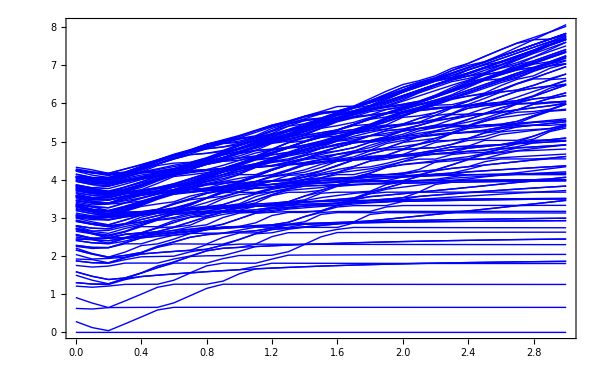

FigSpin

FigSpinOther

```mathematica
Begin["Sub22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### export

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S05"<>".pdf" }],   Ada22S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S05"<>".pdf"  }],  Ada22S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S1"<>".pdf"  }],  Ada22S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S1"<>".pdf"  }],  Ada22S1`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S15"<>".pdf" }],   Ada22S15`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S15"<>".pdf"  }],  Ada22S15`FigSpin ];
```

### XXZ FM SUB (3,3)

#### code spin 1/2

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Sub33S05`"]; 

$FileName="XXZ.m";
systemDimensions = {{3,3}};
kitaev                = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1cvec};
hfields               = {0.5 cvec};
impuritySpin    = {1/2};
gs                            = {1};
KondoCouplings   = {0,1,.01};
parameters          = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 2;
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,PlotRange-> plotRange ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6},(*{colour,4},*){colour,6}};
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]](* ,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{ Scaled[{0.02,0.01}],Scaled[{0,0}]} ]     ];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
];
End[]
```

```mathematica
Begin["Sub33S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code spin 1

```mathematica
ClearAll[figEn]
```

```mathematica
Begin["Sub33S1`"]; 

$FileName="XXZ.m";
systemDimensions = {{3,3}};
kitaev                = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1cvec};
hfields               = {0.5 cvec};
impuritySpin    = {1};
gs                            = {1};
KondoCouplings   = {0,1,.01};
parameters          = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 2;
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
dataName2=Module[{i,f,δ,k}, 	{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};				
StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ";
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.98,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|","\\omega/|J|"},ImageSize->600,PlotRange-> plotRange ] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]

Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= "XXZ"; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6},(*{colour,4},*){colour,6}};
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]](* ,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{ Scaled[{0.02,0.01}],Scaled[{0,0}]} ]     ];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
];
End[]
```

```mathematica
Begin["Sub33S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### export

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Sub33S05"<>".pdf" }],   Sub33S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Sub33S05"<>".pdf"  }],  Sub33S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Sub33S1"<>".pdf"  }],  Sub33S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Sub33S1"<>".pdf"  }],  Sub33S1`FigSpin ];
```

## Spin operators Adatom

### Heisenberg FM (2,2)

#### code spin 1/2

```mathematica
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1{1,1,1}};
hfields          = {0.5 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,1,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;
HamCoupling="XXZ_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Length@KondoCouplings


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];

	plotTitle  = (MaTeX[#,Magnification->1.6]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;

colour=Hue[0.16,1.,1.];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,3},(*{colour,4},*){colour,6}};

Fig22S05=ListPlot[{ dataSimp[[3]][[1;;-1;;2]], dataS1[[3]][[1;;-1;;2]], dataS2[[1]][[1;;-1;;2]],(*dataS2[[2]],*) dataS2[[3]][[1;;-1;;2]]},
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },
After (*{1.01,.5}*)]]

]
```

```mathematica
Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}]
```

#### code spin 3/2

```mathematica
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1{1,1,1}};
hfields          = {0.5 cvec};
impuritySpin     = {3/2};
gs               = {1};
KondoCouplings   = {0,1,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;
HamCoupling="XXZ_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Length@KondoCouplings


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];

	plotTitle  = (MaTeX[#,Magnification->1.6]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;

colour=Hue[0.16,1.,1.];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,3},(*{colour,4},*){colour,6}};

Fig22S05=ListPlot[{ dataSimp[[3]][[1;;-1;;2]], dataS1[[3]][[1;;-1;;2]], dataS2[[1]][[1;;-1;;2]],(*dataS2[[2]],*) dataS2[[3]][[1;;-1;;2]]},
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },
After (*{1.01,.5}*)]]

]
```

```mathematica
Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}]
```

#### export

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigAdatom22-S=0.5.pdf" }],    Fig22S05, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigAdatom22-S=1.pdf" }],    Fig22S1, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigAdatom22-S=1.5.pdf" }],    Fig22S15, ImageSize->600,ImageResolution->400];
```

### Kitaev FM (3,3)

#### code spin 1/2

```mathematica
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,1,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";	
markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig33S05=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]]

]
```

#### code spin 1

```mathematica
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,2,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;	
markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig33S1=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]]
]
```

#### code spin 3/2

```mathematica
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {3/2};
gs               = {1};
KondoCouplings   = {0,1,.05};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["adatomLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=3/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;	
markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig33S15=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]]
]
```

#### export

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigAdatom33-S=0.5.pdf" }],    Fig33S05, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigAdatom33-S=1.pdf" }],    Fig33S1, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigAdatom33-S=1.5.pdf" }],    Fig33S15, ImageSize->600,ImageResolution->400];
```

## Spin operators Substitution

### Kitaev FM (2,2)

#### code spin 1/2

```mathematica
systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["substitutionLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";	
markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig22S05=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]]

]
```

#### code spin 1

```mathematica
systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["substitutionLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";	
markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig22S1=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]]

]
```

#### code spin 3/2

```mathematica
systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {3/2};
gs               = {1};
KondoCouplings   = {0,1,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;
HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};
	scriptName= StringReplace["substitutionLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "K=-1, \\; S_{\\text{imp}}=3/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";	
markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig22S15=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]];

]
```

#### export

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution22-S=0.5.pdf" }],    Fig22S05, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution22-S=1.pdf" }],    Fig22S1, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution22-S=1.5.pdf" }],    Fig22S15, ImageSize->600,ImageResolution->400];
```

### Kitaev FM (3,3)

#### code spin 1/2

```mathematica
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = {0,.5,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["substitutionLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp  =Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;

	plotLegend= "K=-1, \\; S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";
	

Fig33Sa=ListPlot[{dataSimp[[1]],dataSbulk[[1]]},
PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{a}}\\rangle"},ImageSize->600,PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]];

Fig33Sb=ListPlot[{dataSimp[[2]],dataSbulk[[2]]},
PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{b}}\\rangle"},ImageSize->600,PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]];

Fig33Sc=ListPlot[{dataSimp[[3]],dataSbulk[[3]]},
PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{c}}\\rangle"},ImageSize->600,PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]];


markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig33S=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]]

]
```

#### code spin 1

```mathematica
systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1};
gs               = {1};
KondoCouplings   =  {0,.5,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 100;

HamCoupling="Kitaev_FM";
dataName=Module[{i,f,δ,k}, 
				{i,f,δ}=KondoCouplings;  k=klevels;    {i,f,δ,k}=ToString/@{i,f,δ,k};
				StringReplace["JK=Range[i,f,d]", {"i"->i,"f"->f,"d"->δ,"k0"->k}]  ];
KondoCouplings=Range@@KondoCouplings;


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSbulk,dataSimp},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};

	scriptName= StringReplace["substitutionLXLY",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  StringJoin[dataPath[StringJoin[dataName,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder],".txt"];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataSbulk=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];

	plotTitle  = (MaTeX[#,Magnification->1.5]&)@StringReplace["K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}, \\,  (L_x,L_y)=(LX,LY)",{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= "K=-1, \\; S_{\\text{imp}}=1, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";	

Fig33SaS1=ListPlot[{dataSimp[[1]],dataSbulk[[1]]},
PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{a}}\\rangle"},ImageSize->600,PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]];

Fig33SbS1=ListPlot[{dataSimp[[2]],dataSbulk[[2]]},
PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{b}}\\rangle"},ImageSize->600,PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]];

Fig33ScS1=ListPlot[{dataSimp[[3]],dataSbulk[[3]]},
PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{c}}\\rangle"},ImageSize->600,PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]];

markers=opensMarker/@Tuples[{{Hue[197/360,.7,1],Hue[347/360,.4,1] },{3,4,6}}];

Fig33S1=ListPlot[{dataSimp[[1]],dataSimp[[2]],dataSimp[[3]],dataSbulk[[1]],dataSbulk[[2]],dataSbulk[[3]]},
PlotStyle->{Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[197/360,.7,1],Hue[347/360,.4,1],Hue[347/360,.4,1],Hue[347/360,.4,1] },PlotMarkers-> Tuples@{markers,{Scaled[0.03]}},Joined->True,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{bulk} }} \\cdot \\hat{\\mathbf{c}}\\rangle  "         },
After (*{1.01,.5}*)]];

]
```

```mathematica
(*SwatchLegend["Expressions",  LegendFunction->(Framed[#,Background->Lighter[Gray, 0.5] ]&)]  *)
```

#### export

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-S=0.5.pdf" }],    Fig33S, ImageSize->600,ImageResolution->400];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-S=1.pdf" }],    Fig33S1, ImageSize->600,ImageResolution->400];
```

```mathematica
(*Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-Sa-S=0.5.pdf" }],    Fig33Sa, ImageSize->600,ImageResolution->400]; 
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-Sb-S=0.5.pdf" }],    Fig33Sb, ImageSize->600,ImageResolution->400]; 
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-Sc-S=0.5.pdf" }],    Fig33Sc, ImageSize->600,ImageResolution->400]; *)
```

```mathematica
(*Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-Sa-S=1.pdf" }],    Fig33SaS1, ImageSize->600,ImageResolution->400]; 
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-Sb-S=1.pdf" }],    Fig33SbS1, ImageSize->600,ImageResolution->400]; 
Export[     FileNameJoin[{ figFolder,"Spin Operators","FigSubstitution33-Sc-S=1.pdf" }],    Fig33ScS1, ImageSize->600,ImageResolution->400]; *)
```

## Spin operators

Compute expectation values of spin operators. 
First take component along the c direction.

```mathematica
Ns=30;
JKmax=1;
dJK=JKmax/Ns;
For[i=0,i≤Ns,i++,
JK0=i dJK;
R=Chop[Eigensystem[N[H[JK0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[JK0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mbulk=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] 1/2 Subscript[σ, n],{n,1,3}],IdS].Ψ[1];
Mimplist[i]=Chop[N[{JK0,Mimp}]];
Mbulklist[i]=Chop[N[{JK0,Mbulk}]]];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMbulk=Table[Mbulklist[i],{i,0,Ns}];
```

```mathematica
ListPlot[{listMimp,listMbulk},PlotStyle->{Blue,Red},Joined->False,Frame->True,PlotRange->All,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{c}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->1.8]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]]
```

Now the in-plane component along the a direction. 
This component is always zero for the impurity spin and the site to which it is coupled. 
Consider  j=3 as a neighboring site that shows the vortex-like pattern.

```mathematica
dJK=JKmax/Ns;
For[i=0,i≤Ns,i++,
JK0=i dJK;
R=Chop[Eigensystem[N[H[JK0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[JK0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Id,Sum[avec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mneigh=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Sum[avec[[n]] 1/2 Subscript[σ, n],{n,1,3}],Id,Id,Id,Id,Id,IdS].Ψ[1];
Mimplist[i]=Chop[N[{JK0,Mimp}]];
Mneighlist[i]=Chop[N[{JK0,Mneigh}]]];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMneigh=Table[Mneighlist[i],{i,0,Ns}];
```

```mathematica
ListPlot[{listMimp,listMneigh},PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{a}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->1.8]&)/@{"\\text{impurity}","\\text{bulk}, j=3"},{.8,.7}]]
```